```mathematica
(* initial data *)
mt=0.1; (* modeling time *)
l=1; (* string length *)
j=10000; (* time steps *)
i=10;(* length steps *)
v=10; (* propagation speed perturbations along the string *)
```

```mathematica
(* auxiliary variables *)
dt=mt/j;
dx=l/i;
g=dt/dx;
ms=IntegerPart[3*l/(4*dx)]; (* max stretching index *)
```

```mathematica
(* create array, containing string stretching *)
u={};
```

```mathematica
(* ui0 *)
ui0[]:=
Module[{buffer,k},
buffer={};
Do[If[k==ms,buffer=Append[buffer,1],
If[k>ms,buffer=Append[buffer,-4 *k* dx/l+4],buffer=Append[buffer,4* k* dx/(3*l)]]]
,{k,0,i}];
u=Append[u,buffer];
]
```

```mathematica
(* ui1 *)
ui1[]:=
Module[{buffer,k},
buffer={};
Do[If[k==ms,buffer=Append[buffer,1-dx],
If[k>ms,buffer=Append[buffer,(1-dx)(-4 *k* dx/l+4)],buffer=Append[buffer,(1-dx)(4* k* dx/(3*l))]]]
,{k,0,i}];
u=Append[u,buffer];
]
```

```mathematica
(* uij *)
uij[]:=
Module[{buffer,k,p},
Do[
If[IntegerPart[p/200]==0,Print["j = ",p-1]];
buffer={};
buffer=Append[buffer,0];
Do[buffer=Append[buffer,g^2/v^2 *(u[[p-1,k-1]]+u[[p-1,k+1]])-u[[p-2,k]]+2*(1-g^2/v^2)* u[[p-1,k]]]
,{k,1,i-1}];
buffer=Append[buffer,0];
u=Append[u,buffer];
,{p,3,j}];
]
```

```mathematica
(* fill the array *)
ui0[];
ui1[];
uij[];
```

j = 2

j = 3

j = 4

j = 5

j = 6

j = 7

j = 8

j = 9

j = 10

j = 11

j = 12

j = 13

j = 14

j = 15

j = 16

j = 17

j = 18

j = 19

j = 20

j = 21

j = 22

j = 23

j = 24

j = 25

j = 26

j = 27

j = 28

j = 29

j = 30

j = 31

j = 32

j = 33

j = 34

j = 35

j = 36

j = 37

j = 38

j = 39

j = 40

j = 41

j = 42

j = 43

j = 44

j = 45

j = 46

j = 47

j = 48

j = 49

j = 50

j = 51

j = 52

j = 53

j = 54

j = 55

j = 56

j = 57

j = 58

j = 59

j = 60

j = 61

j = 62

j = 63

j = 64

j = 65

j = 66

j = 67

j = 68

j = 69

j = 70

j = 71

j = 72

j = 73

j = 74

j = 75

j = 76

j = 77

j = 78

j = 79

j = 80

j = 81

j = 82

j = 83

j = 84

j = 85

j = 86

j = 87

j = 88

j = 89

j = 90

j = 91

j = 92

j = 93

j = 94

j = 95

j = 96

j = 97

j = 98

j = 99

j = 100

j = 101

j = 102

j = 103

j = 104

j = 105

$Aborted

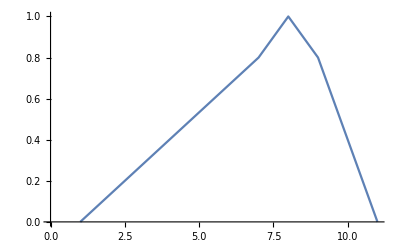

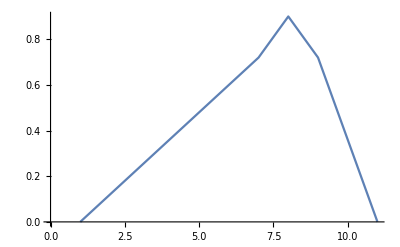

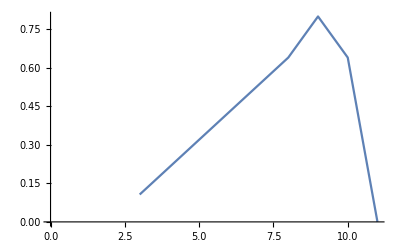

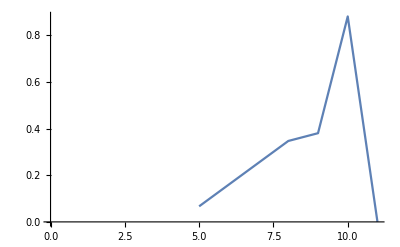

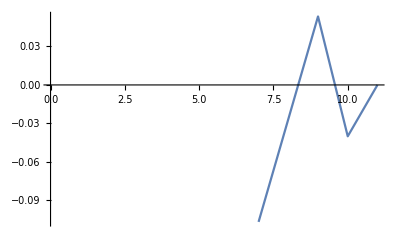

-Graphics-

```mathematica
(* visualization *)
ListLinePlot[u[[1]]]
ListLinePlot[u[[2]]]
ListLinePlot[u[[3]]]
ListLinePlot[u[[4]]]
ListLinePlot[u[[5]]]
ListLinePlot[u[[10]]]
```